```mathematica
ClearAll["Global`*"]
```

```mathematica
34/2
```

17

```mathematica
dq = Sqrt[6/(m h) Log[2 N/d]]
```

√6 √(Log[(2 N)/d]/(h m))

```mathematica
dq /. h -> 24 m Log[4N/d]
```

1/2 √(Log[(2 N)/d]/(m^2 Log[(4 N)/d]))

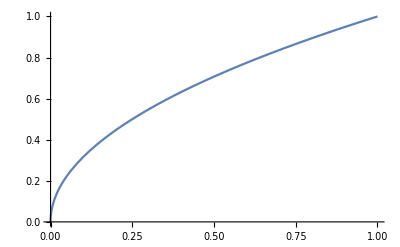

```mathematica
Plot[Sqrt[x],{x,0,1}]
```

```mathematica
N[(2^(2/3)10000^(1/3))]
```

34.1995

```mathematica
D[Exp[-x],x]
```

-ⅇ^-x

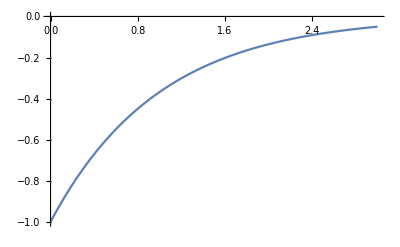

```mathematica
Plot[-ⅇ^-x,{x,0,3}]
```

```mathematica
L = t1(t-t1)/(t1(1-q)^2+(t-t1)q^2)
```

((t-t1) t1)/(q^2 (t-t1)+(1-q)^2 t1)

```mathematica
((t-t1) t1)/(q^2 (t-t1)+(1-q)^2 t1)
```

((t-t1) t1)/(q^2 (t-t1)+(1-q)^2 t1)

```mathematica
D[L,t1]
```

-(((1-q)^2-q^2) (t-t1) t1)/((q^2 (t-t1)+(1-q)^2 t1)^2)+(t-t1)/(q^2 (t-t1)+(1-q)^2 t1)-t1/(q^2 (t-t1)+(1-q)^2 t1)

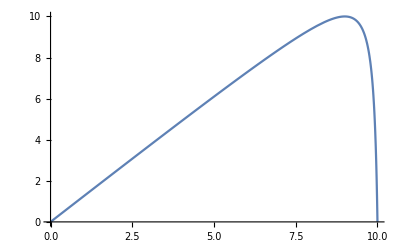

```mathematica
Plot[L /. {t-> 10, q -> 0.9},{t1,0,10}]
```

```mathematica
Maximize[L,t1]
```

{Piecewise[{{t, t>0&&q==1/2}, {-∞, !((t>0&&q==1/2)||(t==0&&q>1/2)||(t==0&&q<1/2)||(t>0&&q>1/2)||(t>0&&q<1/2)||t<0)}, {∞, True}}],{t1→Piecewise[{{Indeterminate, !(t>0&&q==1/2)}, {t/2, True}}]}}

```mathematica
Solve[D[L,t1]==0,t1]
```

```mathematica
{{t1->q t},{t1->(q t)/(-1+2 q)}} /. {q -> .5,t->10}
```

{{t1→6.},{t1→30.}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
L2 = Exp[-A(t1+q*g)]+Exp[-A((t-t1)+(1-q)g)]
```

ⅇ^(-A (g (1-q)+t-t1))+ⅇ^(-A (g q+t1))

```mathematica
Solve[D[L2,t1] == 0,t1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t1→1/2 (g-2 g q+t)}}

```mathematica
D[Exp[-A(t+C)],t]
```

-A ⅇ^(-A (C+t))

```mathematica
D[Exp[-A(B+C*g[x])],x]
```

-A C ⅇ^(-A (B+C g[x])) g'[x]

```mathematica
D[a*t/(b*t+c),t]
```

-(a b t)/(c+b t)^2+a/(c+b t)

```mathematica
Q = t1*t2/(t1(1-q)^2+t2*q^2)
```

(t1 t2)/((1-q)^2 t1+q^2 t2)

```mathematica
D[Q,t1]
```

-((1-q)^2 t1 t2)/(((1-q)^2 t1+q^2 t2)^2)+t2/((1-q)^2 t1+q^2 t2)

```mathematica
ClearAll["Global`*"]
```

Lets try with just two variables

```mathematica
c1 = (t21*t20)/(t21(1-q2)^2+t20*q2^2)
```

(t20 t21)/(q2^2 t20+(1-q2)^2 t21)

```mathematica
c2 = (t11*t10)/(t11*(1-q1)^2+t10*q1^2)
```

(t10 t11)/(q1^2 t10+(1-q1)^2 t11)

```mathematica
f = Exp[-(t11+q1^2*c1)]+Exp[-(t21+q2^2*c2)]+Exp[-(t10+(1-q1)^2*c1)]+Exp[-(t20+(1-q2)^2*c2)]
```

ⅇ^(-((1-q2)^2 t10 t11)/(q1^2 t10+(1-q1)^2 t11)-t20)+ⅇ^(-(q2^2 t10 t11)/(q1^2 t10+(1-q1)^2 t11)-t21)+ⅇ^(-t10-((1-q1)^2 t20 t21)/(q2^2 t20+(1-q2)^2 t21))+ⅇ^(-t11-(q1^2 t20 t21)/(q2^2 t20+(1-q2)^2 t21))

```mathematica
Solve[D[f,t11]==0,t11]
```

Solve[-ⅇ^(-t11-(q1^2 t20 t21)/(q2^2 t20+(1-q2)^2 t21))+ⅇ^(-((1-q2)^2 t10 t11)/(q1^2 t10+(1-q1)^2 t11)-t20) (((1-q1)^2 (1-q2)^2 t10 t11)/((q1^2 t10+(1-q1)^2 t11)^2)-((1-q2)^2 t10)/(q1^2 t10+(1-q1)^2 t11))+ⅇ^(-(q2^2 t10 t11)/(q1^2 t10+(1-q1)^2 t11)-t21) (((1-q1)^2 q2^2 t10 t11)/((q1^2 t10+(1-q1)^2 t11)^2)-(q2^2 t10)/(q1^2 t10+(1-q1)^2 t11))==0,t11]

```mathematica
f2 = f //. {q1->.5,q2->.5,t10->t11,t11->5,t20 -> 10-t21,A->1}
```

ⅇ^(-2.5-t21)+ⅇ^(-12.5+t21)+2 ⅇ^(-5-(0.25 (10-t21) t21)/(0.25 (10-t21)+0.25 t21))

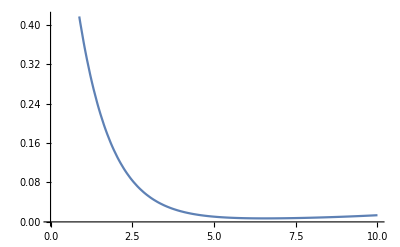

```mathematica
Plot[f //. {q1->.5,q2->0,t10->10-t11,t11->5,t20 -> 10-t21,A->1} ,{t21,0,10}]
```

```mathematica
f3 = f //. {q2 ->1,q1->1}
```

ⅇ^-t10+ⅇ^-t20+2 ⅇ^(-t11-t21)

```mathematica
Solve[D[f3,t21]==0,t21]
```

{{t21→1.33333 (-(1. t10 t11)/(0.25 t10+0.25 t11)-1. Log[-0.25 ⅇ^(-1. t10)-0.25 ⅇ^(-1. t11)])}}

```mathematica
4
```

```mathematica
D[f,t10]
```

-A ⅇ^(-A (t10+((1-q1)^2 t20 t21)/(q2^2 t20+(1-q2)^2 t21)))-A ⅇ^(-A (((1-q2)^2 t10 t11)/(q1^2 t10+(1-q1)^2 t11)+t20)) (-(q1^2 (1-q2)^2 t10 t11)/((q1^2 t10+(1-q1)^2 t11)^2)+((1-q2)^2 t11)/(q1^2 t10+(1-q1)^2 t11))-A ⅇ^(-A ((q2^2 t10 t11)/(q1^2 t10+(1-q1)^2 t11)+t21)) (-(q1^2 q2^2 t10 t11)/((q1^2 t10+(1-q1)^2 t11)^2)+(q2^2 t11)/(q1^2 t10+(1-q1)^2 t11))

```mathematica
ClearAll["Global`*"]
```

```mathematica
T = t1*t0/(t1*(1-q)^2+t0*q^2) //. {t1 -> a,t0->a}
```

```mathematica
a^2/(a (1-q)^2+a q^2)
Simplify[a^2/(a (1-q)^2+a q^2)]
```

a^2/(a (1-q)^2+a q^2)

a/(1-2 q+2 q^2)

```mathematica
h^2/(K^2 ((h (1-q)^2)/K+(h q^2)/K))
FullSimplify[h^2/(K^2 ((h (1-q)^2)/K+(h q^2)/K))]
```

h^2/(K^2 ((h (1-q)^2)/K+(h q^2)/K))

h/(K-2 K q+2 K q^2)

```mathematica
D[T,t1]
```

-(((1-q)^2-q^2) (t-t1) t1)/((q^2 (t-t1)+(1-q)^2 t1)^2)+(t-t1)/(q^2 (t-t1)+(1-q)^2 t1)-t1/(q^2 (t-t1)+(1-q)^2 t1)

```mathematica
Solve[D[T,t1]==0,t1]
```

{{t1→q t},{t1→(q t)/(-1+2 q)}}

```mathematica
T /. t1 -> q t
```

(q t (t-q t))/((1-q)^2 q t+q^2 (t-q t))

```mathematica
N[(4+2Log[2])/3]
```

1.79543

```mathematica
Power[2Exp[-x]]
```

2 ⅇ^-x

```mathematica
PowerExpand[Log[2 ⅇ^-x]]
```

-x+Log[2]

```mathematica
PowerExpand[Log[ⅇ^-x]]
```

-x

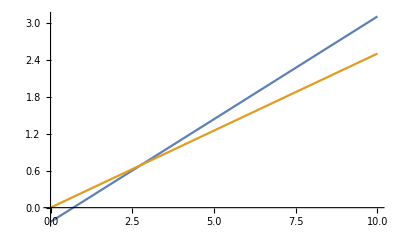

```mathematica
Plot[{(c-Log[2])/3,c/4},{c,0,10}]
```

```mathematica
Minimize[{Exp[-x]+Exp[-y],x+y==1},{x,y}]
```

Minimize[{ⅇ^-x+ⅇ^-y,x+y==1},{x,y}]

```mathematica
Minimize[{Exp[-x]+Exp[-y],y+x==c},{x,y}]
```

```mathematica
Minimize[{x^2+2y^2,x+y==c,x > 0,y > 0},{x,y}]
```

{Piecewise[{{(2 c^2)/3, c>0}, {∞, True}}],{x→Piecewise[{{(2 c)/3, c>0}, {Indeterminate, True}}],y→Piecewise[{{c/3, c>0}, {Indeterminate, True}}]}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
D[Exp[-A(x+c)],x]
```

-A ⅇ^(-A (c+x))

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]

```mathematica
D[Exp[-A(t+q*g[x])],x]
```

-A ⅇ^(-A (t+q g[x])) q g'[x]

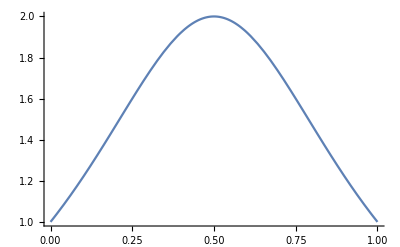

```mathematica
Plot[1/((1-q)^2+q^2),{q,0,1}]
```

```mathematica
f = Exp[-A(b+c q^2)]+Exp[-A(b+c (1-q)^2)]
```

ⅇ^(-A (b+c (1-q)^2))+ⅇ^(-A (b+c q^2))

```mathematica
Solve[D[f,q]==0,q]
```

Solve[2 A c ⅇ^(-A (b+c (1-q)^2)) (1-q)-2 A c ⅇ^(-A (b+c q^2)) q==0,q]

```mathematica
Plot[f //.{A->1,b->.1,c->100},{q,0,q}]
```

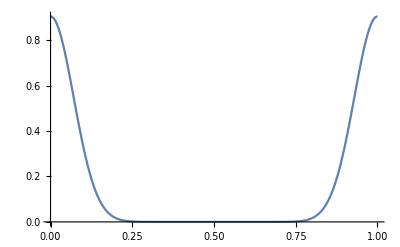

```mathematica
Plot[f//.{A->1,b->0.1,c->100},{q,0,1}]
```

```mathematica
f //.{A->1,b->.1,c->100}
```

ⅇ^(-0.1-100 (1-q)^2)+ⅇ^(-0.1-100 q^2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
f = Exp[-A(t11+2(N-1)t)]+Exp[-A t10]+2(N-1)Exp[-A(t(1+(N-2)/2)+t11/4)]
```

ⅇ^(-A t10)+ⅇ^(-A (2 (-1+N) t+t11))+2 ⅇ^(-A ((1+1/2 (-2+N)) t+t11/4)) (-1+N)

```mathematica
D[f,t11]
```

-A ⅇ^(-A (2 (-1+N) t+t11))-1/2 A ⅇ^(-A ((1+1/2 (-2+N)) t+t11/4)) (-1+N)

```mathematica
PowerExpand[Log[Exp[-A t10]]]
```

-A t10

```mathematica
PowerExpand[Log[x/y]]
```

Log[x]-Log[y]

```mathematica
Solve[(N-1)/2 == (N+6)/8,N]
```

{{N→10/3}}

```mathematica
1+(N-2)/8 ==(N+6)/8
```

1+1/8 (-2+N)==(6+N)/8

```mathematica
8/8+(N-2)/8
```

1+1/8 (-2+N)

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[l== A Exp[-t10],t10]
```

{{t10→ConditionalExpression[2 ⅈ π C[1]+Log[A/l],C[1]∈Integers]}}

```mathematica
f = Exp[-A t]+(C)*Exp[-A/4(h-t)]
```

C ⅇ^(-1/4 A (h-t))+ⅇ^(-A t)

```mathematica
Solve[D[f,t]==0,t]
```

{{t→(A h+4 Log[4/C])/(5 A)}}

```mathematica
(A h+4 Log[4/C])/(5 A) //. {C -> 2(N-1)+1,N -> 100,h-> 500,A->.1}
```

68.7439

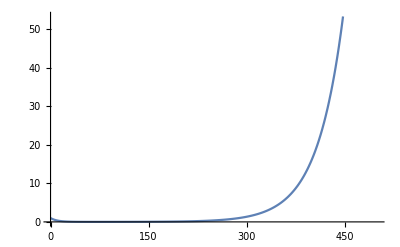

```mathematica
Plot[f //. {C -> 2(N-1)+1,N -> 100,h-> 500,A->.1},{t,0,500}]
```

```mathematica
D[f,t]
```

1/4 A C ⅇ^(-1/4 A (h-t))-A ⅇ^(-A t)

```mathematica
Log[A*B]
```

Log[A B]

```mathematica
Minimize[{f,t > 0}{t}]
```

Minimize[{t} {C ⅇ^(-1/4 A (h-t))+ⅇ^(-A t),t>0}]

```mathematica
Click for copyable input
```

```mathematica
Minimize[{x,x^2+y^2<1},{x,y}]
```

{-1,{x→-1,y→0}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[(a+b)(a+d) - a == 0 /. d -> 1/2 (1-b-c-√(-4 b c+(-1+b+c)^2)),a]
```

{{a→1/4 (1-b+c+√(-4 b c+(-1+b+c)^2)-√((-1+b-c-√(-4 b c+(-1+b+c)^2))^2-8 (b-b^2-b c-b √(-4 b c+(-1+b+c)^2))))},{a→1/4 (1-b+c+√(-4 b c+(-1+b+c)^2)+√((-1+b-c-√(-4 b c+(-1+b+c)^2))^2-8 (b-b^2-b c-b √(-4 b c+(-1+b+c)^2))))}}

```mathematica
Solve[(c+d)(b+d)-d==0,d]
```

{{d→1/2 (1-b-c-√(-4 b c+(-1+b+c)^2))},{d→1/2 (1-b-c+√(-4 b c+(-1+b+c)^2))}}

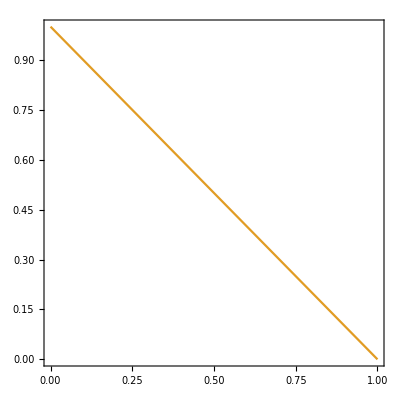

```mathematica
ContourPlot[{Exp[-A x]+Exp[- A y] //. {A -> 3}, x + y == 1},{x,0,1},{y,0,1}]
```

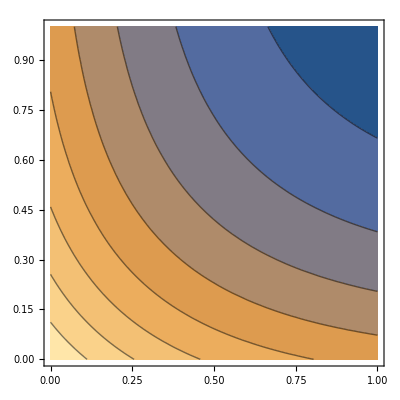

```mathematica
ContourPlot[{Exp[-2 x]+Exp[-2y] },{x,0,1},{y,0,1}]
```

```mathematica
Minimize[Exp[-x]+Exp[-(h-x)],x]
```

Minimize[ⅇ^-x+ⅇ^(-h+x),x]

```mathematica
Solve[D[Exp[-A x]+Exp[-A(h-2*x)],x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(A h-Log[2])/(3 A)}}

```mathematica
D[Exp[-x]+Exp[-(h-2*x)],x]
```

-ⅇ^-x+2 ⅇ^(-h+2 x)

```mathematica
PowerExpand[Log[Exp[-A x]]]
```

-A x

```mathematica
c =t1*t2/(t1(1-q)^2+t2*q^2)
```

(t1 t2)/((1-q)^2 t1+q^2 t2)

```mathematica
c //. {t1->t2,q->.5}
```

2. t2

```mathematica
t + (1/4)(t11+2(N-2)t)
```

t+1/4 (2 (-2+N) t+t11)

```mathematica
Expand[t + (1/4)(t11+2(N-2)t)]
```

(N t)/2+t11/4

```mathematica
Simplify[%43]
```

1/4 (2 (1+N) t+t11)

```mathematica
ExpandAll[%46]
```

t/2+(N t)/2+t11/4

```mathematica
Together[t+((N-2) t)/2]
```

(N t)/2

ProductExpand[t+1/4 (2 (-1+N) t+t11)]

```mathematica
Reduce[2(N-1)>N/2,N]
```

N>4/3

```mathematica
Simplify[2*(N-1)+1]
```

-1+2 N

```mathematica
ClearAll["Global`*"]
```

```mathematica
T = t11/4+N t/2
```

(N t)/2+t11/4

```mathematica
Solve[t11+2(N-1)t == h,t]
```

{{t→(h-t11)/(2 (-1+N))}}

```mathematica
T /. t->(h-t11)/(2 (-1+N))
```

(N (h-t11))/(4 (-1+N))+t11/4

```mathematica
%81 /. t11 -> 0
```

(h N)/(4 (-1+N))

```mathematica
%81 /. t11 -> 1
```

1/4+((-1+h) N)/(4 (-1+N))

```mathematica
Simplify[%84]
```

(1-h N)/(4-4 N)

```mathematica
T //. {t11 -> 0,t->(h-t11)/(2 (-1+N))}
```

(h N)/(4 (-1+N))

```mathematica
T //. {t11 -> 1,t->(h-t11)/(2 (-1+N))}
```

1/4+((-1+h) N)/(4 (-1+N))

```mathematica
Simplify[%90]
```

(1-h N)/(4-4 N)

```mathematica
q = x+1/2
```

1/2+x

```mathematica
q^2
```

(1/2+x)^2

```mathematica
Expand[(1-q)^2]
```

1/4-x+x^2

```mathematica
Expand[(1/2+x)^2]
```

1/4+x+x^2

```mathematica
ClearAll["Global`*"]
```

```mathematica
f = N1*Exp[-A(t1+(1/4+x+x^2)c1)]+2*N2*Exp[-A(t+(1/4-x+x^2)c2)]
```

ⅇ^(-A (t1+c1 (1/4+x+x^2))) N1+2 ⅇ^(-A (t+c2 (1/4-x+x^2))) N2

```mathematica
f2 = f //. {c1 -> (N1)t1/(1/4+x+x^2) + N2*t/(1/2-x+x^2),c2 -> N*t1/(1/4+x+x^2) + (N2)*t/(1/2-x+x^2)}
```

ⅇ^(-A (t1+(1/4+x+x^2) ((N2 t)/(1/2-x+x^2)+(N1 t1)/(1/4+x+x^2)))) N1+2 ⅇ^(-A (t+(1/4-x+x^2) ((N2 t)/(1/2-x+x^2)+(N t1)/(1/4+x+x^2)))) N2

```mathematica
Solve[N1*t1+2N2*t - h ==0,t1]
```

{{t1→(h-2 N2 t)/N1}}

```mathematica
f3 = f2/. t1->(h-2 N2 t)/N1
```

ⅇ^(-A ((h-2 N2 t)/N1+(1/4+x+x^2) ((N2 t)/(1/2-x+x^2)+(h-2 N2 t)/(1/4+x+x^2)))) N1+2 ⅇ^(-A (t+(1/4-x+x^2) ((N2 t)/(1/2-x+x^2)+(N (h-2 N2 t))/(N1 (1/4+x+x^2))))) N2

```mathematica
f4 = f3 /. N2 -> N-N1
```

2 ⅇ^(-A (t+(1/4-x+x^2) (((N-N1) t)/(1/2-x+x^2)+(N (h-2 (N-N1) t))/(N1 (1/4+x+x^2))))) (N-N1)+ⅇ^(-A ((h-2 (N-N1) t)/N1+(1/4+x+x^2) (((N-N1) t)/(1/2-x+x^2)+(h-2 (N-N1) t)/(1/4+x+x^2)))) N1

```mathematica
Solve[D[f4,t]==0,t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-A ⅇ^(-A ((h-2 (N-N1) t)/N1+(1/4+x+x^2) (((N-N1) t)/(1/2-x+x^2)+(h-2 (N-N1) t)/(1/4+x+x^2)))) N1 (-(2 (N-N1))/N1+(1/4+x+x^2) ((N-N1)/(1/2-x+x^2)-(2 (N-N1))/(1/4+x+x^2)))-2 A ⅇ^(-A (t+(1/4-x+x^2) (((N-N1) t)/(1/2-x+x^2)+(N (h-2 (N-N1) t))/(N1 (1/4+x+x^2))))) (N-N1) (1+(1/4-x+x^2) ((N-N1)/(1/2-x+x^2)-(2 N (N-N1))/(N1 (1/4+x+x^2))))==0,t]

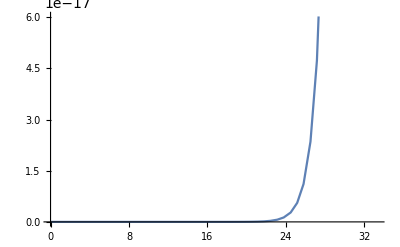

```mathematica
Plot[2 ⅇ^(-A (t+(1/4-x+x^2) (((N-N1) t)/(1/2-x+x^2)+(N (h-2 (N-N1) t))/(N1 (1/4+x+x^2))))) (N-N1)+ⅇ^(-A ((h-2 (N-N1) t)/N1+(1/4+x+x^2) (((N-N1) t)/(1/2-x+x^2)+(h-2 (N-N1) t)/(1/4+x+x^2)))) N1 //.{A-> 1/16,x -> 0,N-> 20,N1-> 10,h-> 1000},{t,0,1000/(2*20-10)}]
```

```mathematica
2 ⅇ^(-A (t+(1/4-x+x^2) (((N-N1) t)/(1/2-x+x^2)+(N (h-2 (N-N1) t))/(N1 (1/4+x+x^2))))) (N-N1)+ⅇ^(-A ((h-2 (N-N1) t)/N1+(1/4+x+x^2) (((N-N1) t)/(1/2-x+x^2)+(h-2 (N-N1) t)/(1/4+x+x^2)))) N1 //.{x -> 1/4,N-> 20,N1-> 10,h-> 1000}
```

10 ⅇ^(-A (1/10 (1000-20 t)+9/16 (16/9 (1000-20 t)+32 t)))+20 ⅇ^(-A (t+1/16 (32/9 (1000-20 t)+32 t)))

```mathematica
Collect[t+(1/4-x+x^2) (((N-N1) t)/(1/2-x+x^2)+(N (h-2 (N-N1) t))/(N1 (1/4+x+x^2))),t]
```

(h N (1/4-x+x^2))/(N1 (1/4+x+x^2))+t (1+((N-N1) (1/4-x+x^2))/(1/2-x+x^2)-(2 N (N-N1) (1/4-x+x^2))/(N1 (1/4+x+x^2)))

```mathematica
Collect[(h-2 (N-N1) t)/N1+(1/4+x+x^2) (((N-N1) t)/(1/2-x+x^2)+(h-2 (N-N1) t)/(1/4+x+x^2)),t]
```

h+h/N1+t (-2 (N-N1)-(2 (N-N1))/N1+((N-N1) (1/4+x+x^2))/(1/2-x+x^2))

```mathematica
f4 /. t-> 0
```

2 ⅇ^(-(A h N (1/4-x+x^2))/(N1 (1/4+x+x^2))) (N-N1)+ⅇ^(-A (h+h/N1)) N1

```mathematica
f4 /. t-> h/2(N-N1)
```

2 ⅇ^(-A (1/2 h (N-N1)+(1/4-x+x^2) ((h (N-N1)^2)/(2 (1/2-x+x^2))+(N (h-h (N-N1)^2))/(N1 (1/4+x+x^2))))) (N-N1)+ⅇ^(-A ((h-h (N-N1)^2)/N1+(1/4+x+x^2) ((h (N-N1)^2)/(2 (1/2-x+x^2))+(h-h (N-N1)^2)/(1/4+x+x^2)))) N1

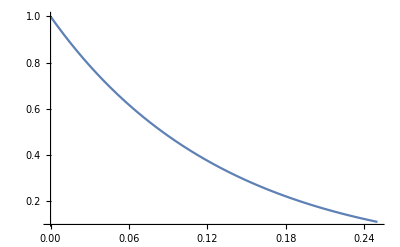

```mathematica
Plot[(1/4-x+x^2)/(1/4+x+x^2),{x,0,1/4}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[N1*t0+N1*t1+2*N2*t - h ==0, t]
```

{{t→(h-N1 t0-N1 t1)/(2 N2)}}

```mathematica
Solve[N1*t0+N1*t1+2*N2*t - h ==0, t0]
```

{{t0→(h-2 N2 t-N1 t1)/N1}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
F =2Exp[-A(t+1/4(N-1)t11)]+(N-1)Exp[-A(2t+(N-1)t11)]
```

2 ⅇ^(-A (t+1/4 (-1+N) t11))+ⅇ^(-A (2 t+(-1+N) t11)) (-1+N)

```mathematica
Solve[2t+(N-1)t11 - l == 0,t]
```

{{t→1/2 (l+t11-N t11)}}

```mathematica
Solve[2t+(N-1)t11 - l == 0,t11]
```

{{t11→(l-2 t)/(-1+N)}}

```mathematica
f2 = F /. t->1/2 (l+t11-N t11)
```

2 ⅇ^(-A (1/4 (-1+N) t11+1/2 (l+t11-N t11)))+ⅇ^(-A (l+t11+(-1+N) t11-N t11)) (-1+N)

```mathematica
Solve[D[f2,t11]==0,t11]
```

{}

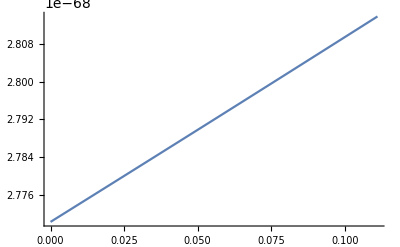

```mathematica
Plot[f2 //. {A -> 1/16,l-> 5000,N->10},{t11,0,1/(9)}]
```

```mathematica
f2 /. t11 -> 0
```

2 ⅇ^(-(A l)/2)+ⅇ^(-A l) (-1+N)

```mathematica
f2 /. t11 -> 1/(N-1)
```

2 ⅇ^(-A (1/4+1/2 (l+1/(-1+N)-N/(-1+N))))+ⅇ^(-A (1+l+1/(-1+N)-N/(-1+N))) (-1+N)

```mathematica
ClearAll["Global`*"]
```

```mathematica
g = a x + b y
```

a x+b y

```mathematica
Solve[w1 x+w2 y -c ==0,y]
```

{{y→(c-w1 x)/w2}}

```mathematica
g /. y->(c-w1 x)/w2
```

a x+(b (c-w1 x))/w2

```mathematica
Solve[D[2Exp[-A t]+(N-1)Exp[-2A t]+(N-1)Exp[-A((h-2t)/N-1)],t]==0,t]
```

2 ⅇ^(-A t)+ⅇ^(-A (-1+(h-2 t)/N)) (-1+N)+ⅇ^(-2 A t) (-1+N)

```mathematica
f = 2Exp[-A t]+(N-1)Exp[-2A t]+(N-1)Exp[-A((h-2t)/N-1)]
```

2 ⅇ^(-A t)+ⅇ^(-A (-1+(h-2 t)/N)) (-1+N)+ⅇ^(-2 A t) (-1+N)

```mathematica
g = (N+1)Exp[-A t]+(N-1)Exp[-A((h-2t)/N-1)]
```

ⅇ^(-A (-1+(h-2 t)/N)) (-1+N)+ⅇ^(-A t) (1+N)

```mathematica
g1 = g //. {A -> 1/16,N->20,h-> 10000}
```

21 ⅇ^(-t/16)+19 ⅇ^(1/16 (1+1/20 (-10000+2 t)))

```mathematica
f2 = f//. {A -> 1/16,N->20,h-> 10000}
```

19 ⅇ^(-t/8)+2 ⅇ^(-t/16)+19 ⅇ^(1/16 (1+1/20 (-10000+2 t)))

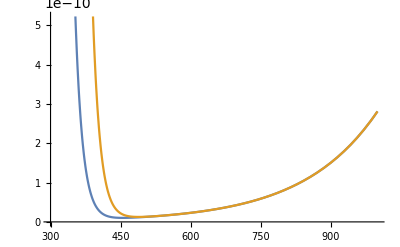

```mathematica
Plot[{f2,g1},{t,300,1000}]
```

```mathematica
Solve[D[(N+1)Exp[-A t]+(N-1)Exp[-A((h-2t)/N-1)],t]==0,t]
```

{{t→(A h-A N-ⅈ N π-N Log[2 A-(2 A)/N]+N Log[-A-A N])/(A (2+N))}}

```mathematica
N[(A h-A N-ⅈ N π-N Log[2 A-(2 A)/N]+N Log[-A-A N])/(A (2+N))//. {A -> 1/16,N->20,h-> 10000}]
```

488.584+0. ⅈ

```mathematica
(A h-A N-ⅈ N π-N Log[2 A-(2 A)/N]+N Log[-A-A N])/(A (2+N))
```

(A h-A N-ⅈ N π-N Log[2 A-(2 A)/N]+N Log[-A-A N])/(A (2+N))

```mathematica
Re[ComplexExpand[(A h-A N-ⅈ N π-N Log[2 A-(2 A)/N]+N Log[-A-A N])/(A (2+N))]]
```

-Im[-(N π)/(A (2+N))-(N Arg[2 A-(2 A)/N])/(A (2+N))+(N Arg[-A-A N])/(A (2+N))]+Re[h/(2+N)-N/(2+N)-(N Log[(2 A-(2 A)/N)^2])/(2 A (2+N))+(N Log[(-A-A N)^2])/(2 A (2+N))]

```mathematica
h/(2+N)-N/(2+N)+(N( Log[(A+A N)^2]- Log[(2 A-(2 A)/N)^2]))/(2 A (2+N)) /. Log[x_]-Log[y_] -> Log[x/y]
```

```mathematica
h/(2+N)-N/(2+N)+(N Log[(A+A N)/(2 A-(2 A)/N)])/(A (2+N))
```

```mathematica
Simplify[(A+A N)/(2 A-(2 A)/N)]
```

(N (1+N))/(2 (-1+N))

```mathematica
N[1/(2+N)(h-N+(N Log[(N(N+1))/(2(N-1))])/A)//. {A -> 1/16,N->20,h-> 10000}]
```

488.584

```mathematica
N[1/(2+N)(h-N+(N Log[N/2])/A)//. {A -> 1/16,N->20,h-> 10000}]
```

487.129

```mathematica
Simplify[g /. t -> 1/(2+N)(h-N+(N Log[N/2])/A)]
```

ⅇ^((A (-h+N)+2 Log[N/2])/(2+N)) (-1+N)+ⅇ^((A (-h+N)-N Log[N/2])/(2+N)) (1+N)

```mathematica
ClearAll["Global`*"]
```

```mathematica
Simplify[t0+(1-2*q)*B /. q->(1/2+x)]
```

t0-2 B x

```mathematica
c = t0*t1/(t1(1-q)^2+t0*q^2)
```

(t0 t1)/(q^2 t0+(1-q)^2 t1)

```mathematica
c //. {t1 -> t0-2 B x,q-> (1/2+x)}
```

(t0 (t0-2 B x))/(t0 (1/2+x)^2+(1/2-x)^2 (t0-2 B x))

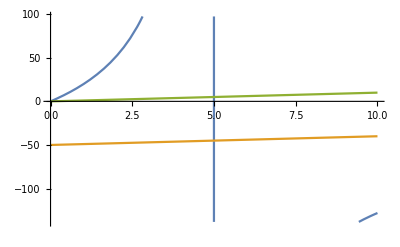

```mathematica
Plot[{(t0 (t0-2 B x))/(t0 (1/2+x)^2+(1/2-x)^2 (t0-2 B x)) //. {B -> 100,x->1/4}, (t0-2 B x)//. {B -> 100,x->1/4}, t0//. {B -> 100,x->1/4}},{t0,0,10}]
```

```mathematica
Solve[D[N*Exp[-A(h-N*t)]+N*Exp[-(A*t)],t]==0,t]
```

{{t→(A h+Log[1/N])/(A (1+N))}}

```mathematica
PowerExpand[Log[1/N]]
```

-Log[N]

```mathematica
f= N1 Exp[-A*t0]+(2N2+N1)Exp[-A((N2+1)/2)t]
```

ⅇ^(-A t0) N1+ⅇ^(-1/2 A (1+N2) t) (N1+2 N2)

```mathematica
Solve[N1*t0+2N2*t -h == 0,t]
```

{{t→(h-N1 t0)/(2 N2)}}

```mathematica
f2 = f /. t->(h-N1 t0)/(2 N2)
```

ⅇ^(-A t0) N1+ⅇ^(-(A (1+N2) (h-N1 t0))/(4 N2)) (N1+2 N2)

```mathematica
Solve[D[f2,t0]==0,t0]
```

{{t0→-(4 N2 Log[(A ⅇ^(-(A h)/4-(A h)/(4 N2)) N1^2+2 A ⅇ^(-(A h)/4-(A h)/(4 N2)) N1 N2+A ⅇ^(-(A h)/4-(A h)/(4 N2)) N1^2 N2+2 A ⅇ^(-(A h)/4-(A h)/(4 N2)) N1 N2^2)/(4 A N1 N2)])/(A (N1+4 N2+N1 N2))}}

```mathematica
Solve[D[X*Exp[-A(a*t)]+Y*Exp[-A(b*t)],t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→Log[-(a X)/(b Y)]/(A (a-b))}}

```mathematica
Solve[D[X*Exp[-A(a*t)]+Y*Exp[-A(b-d*t)],t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(A b+Log[(a X)/(d Y)])/(A (a+d))}}

```mathematica
Apart[(A b+Log[(a X)/(d Y)])/(A (a+d))]
```

b/(a+d)+Log[(a X)/(d Y)]/(A (a+d))

```mathematica
b/(a+d)+Log[(a X)/(d Y)]/(A (a+d)) //. {X -> N1,Y->(2N2+N1),a->1,b->(N2+1)h/4N2,d->(N2+1)N1/4N2}
```

(h N2 (1+N2))/(4 (1+1/4 N1 N2 (1+N2)))+Log[4/(N2 (1+N2) (N1+2 N2))]/(A (1+1/4 N1 N2 (1+N2)))

```mathematica
Expand[4 (1+1/4 N1 N2 (1+N2))]
```

```mathematica
FactorTerms[4+N1 N2+N1 N2^2,N2]
```

4+N1 N2+N1 N2^2

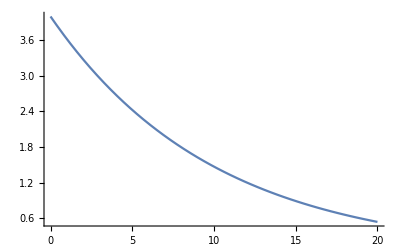

```mathematica
Plot[ X*Exp[-A(a*t)]+Y*Exp[-A(b*t)] //. {A-> .1,X -> 2,Y-> 2,a->1,b->1},{t,0,20}]
```

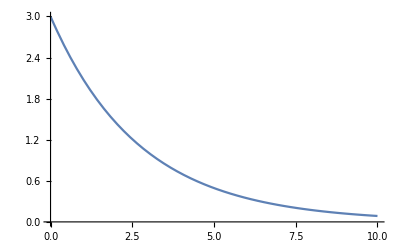

```mathematica
Plot[g,{t,0,10}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
f = N1*Exp[-A(t0)]+(2N2+N1)*Exp[-A((N2+1)/2)t]
```

ⅇ^(-A t0) N1+ⅇ^(-1/2 A (1+N2) t) (N1+2 N2)

```mathematica
Solve[N1*t0+2*N2*t1 - h ==0,t1]
```

{{t1→(h-N1 t0)/(2 N2)}}

```mathematica
f2 = f /. t->(h-N1 t0)/(2 N2)
```

ⅇ^(-A t0) N1+ⅇ^(-(A (1+N2) (h-N1 t0))/(4 N2)) (N1+2 N2)

```mathematica
tout = Simplify[Solve[D[f2,t0]==0,t0]]
```

{{t0→-(4 N2 Log[(ⅇ^(-(A h (1+N2))/(4 N2)) (1+N2) (N1+2 N2))/(4 N2)])/(A (N1+4 N2+N1 N2))}}

```mathematica
tout //. {N1->1,N2->10,h->1000,A->.5}
```

{{t0→212.936}}

```mathematica
tsol = -(4 N2 Log[(ⅇ^(-(A h (1+N2))/(4 N2)) (1+N2) (N1+2 N2))/(4 N2)])/(A (N1+4 N2+N1 N2))
```

-(4 N2 Log[(ⅇ^(-(A h (1+N2))/(4 N2)) (1+N2) (N1+2 N2))/(4 N2)])/(A (N1+4 N2+N1 N2))

```mathematica
Apart[PowerExpand[tsol]]
```

```mathematica
(A h+A h N2+8 N2 Log[2]+4 N2 Log[N2]-4 N2 Log[1+N2])/(A (N1+4 N2+N1 N2))-(4 N2 Log[N1+2 N2])/(A (N1+4 N2+N1 N2)) //. {N1->1,N2->10,h->1000,A->.5}
```

212.936

```mathematica
(h(1+ N2))/(N1+4 N2+N1 N2)+(4 N2 (Log[4]+ Log[N2]- Log[1+N2]- Log[N1+2 N2]))/(A (N1+4 N2+N1 N2))//. {N1->1,N2->10,h->1000,A->.5}
```

212.936

```mathematica
(h(1+ N2))/(N1+4 N2+N1 N2)+(4 N2 (Log[4*N2/((1+N2)(N1+2 N2))]))/(A (N1+4 N2+N1 N2))//. {N1->1,N2->10,h->1000,A->.5}
```

212.936

```mathematica
h(N2+1)/(N1+4N2+N1*N2) + 4N2 Log[4N2/((N2+1)(2N2+N1))]/(A*N1+4N2+N1*N2)
```

```mathematica
(h (1+N2))/(N1+4 N2+N1 N2)+(4 N2 Log[(4 N2)/((1+N2) (N1+2 N2))])/(A (N1+4 N2+N1 N2))//. {N1->10,N2->10,h->1000,A->.01}
```

17.061

```mathematica
(h (1+N2))/(N1+4 N2+N1 N2)-(4 N2 Log[((1+N2) (N1+2 N2))/(4N2)])/(A (N1+4 N2+N1 N2))
```

(h (1+N2))/(N1+4 N2+N1 N2)-(4 N2 Log[((1+N2) (N1+2 N2))/(4 N2)])/(A (N1+4 N2+N1 N2))

```mathematica
f3 = Simplify[f2 /. t0 -> (h (1+N2))/(N1+4 N2+N1 N2)-(4 N2 Log[((1+N2) (N1+2 N2))/(4 N2)])/(A (N1+4 N2+N1 N2))]
```

ⅇ^((-A h (1+N2)+4 N2 Log[((1+N2) (N1+2 N2))/(4 N2)])/(N1+4 N2+N1 N2)) N1+ⅇ^(-((1+N2) (A h+N1 Log[((1+N2) (N1+2 N2))/(4 N2)]))/(N1+4 N2+N1 N2)) (N1+2 N2)

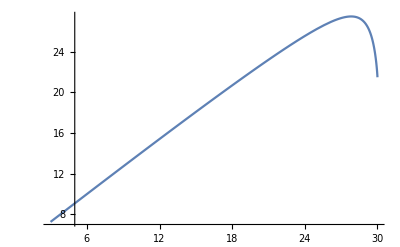

```mathematica
Plot[f3 //. {h -> 10000,A->.001,N2 -> N-N1,N-> 30},{N1,3,30}]
```

```mathematica
Simplify[(h (1+N/2))/((5 N)/2+N^2/4)]-Simplify[(2 N Log[3/4 (1+N/2)])/(A ((5 N)/2+N^2/4))]
```

(2 h (2+N))/(N (10+N))-(8 Log[(3 (2+N))/8])/(A (10+N))

```mathematica
Simplify[(2 h)/(2+2 N)]-Simplify[(4 Log[(1+N)/2])/(A (2+2 N))]
```

h/(1+N)-(2 Log[(1+N)/2])/(A (1+N))

```mathematica
Simplify[(h N)/(4 (-1+N)+N)]-Simplify[(4 (-1+N) Log[((1+2 (-1+N)) N)/(4 (-1+N))])/(A (4 (-1+N)+N))]
```

(h N)/(-4+5 N)-(4 (-1+N) Log[(N-2 N^2)/(4-4 N)])/(A (-4+5 N))

```mathematica
(h (1+N2))/(N1+4 N2+N1 N2)//. {N1->10,N2->10.0,h->1000,A->.1}
```

73.3333

```mathematica
f1 = h/(N/2+5)-4Log[N/2]/(A(N/2+5))
```

h/(5+N/2)-(4 Log[N/2])/(A (5+N/2))

```mathematica
f2 = h/N-2 Log[N/2]/(A*N)
```

h/N-(2 Log[N/2])/(A N)

```mathematica
f3 = h/5 - 4/(5A) Log[N/2]
```

h/5-(4 Log[N/2])/(5 A)

This Plot describes, if we look at different scenarios of how unbalanced the q’s are, the relationship between how f

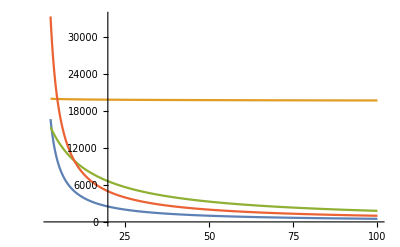

```mathematica
Plot[{100000/(2N),f3//.{A->.01,h->100000},f1//.{A->.01,h->100000},f2//.{A->.01,h->100000}},{N,3,100}]
```

```mathematica
Plot[tout //. {N1->5,N2->10,h->10000,A->.1},{t0,0,10000}]
```

-Graphics-

```mathematica
FactorTerms[(A (1+N2) (h-N1 t0))/(4 N2),t0]
```

1/4 (A h+(A h)/N2-A N1 t0-(A N1 t0)/N2)

```mathematica
Simplify[Together[A h+(A h)/N2]]
```

(A h (1+N2))/N2

```mathematica
Simplify[Together[A N1 -(A N1)/N2]]
```

(A N1 (-1+N2))/N2

```mathematica
ⅇ^(-A t0) N1+ⅇ^(-A((h (1+N2))/(4N2)-(N1 (-1+N2)t0)/(4N2))) (N1+2 N2)
```

```mathematica
b/(a+d)+Log[(a X)/(d Y)]/(A (a+d)) //. {X -> N1,Y->(2N2+N1),a->1,b->(N2+1)h/4N2,d->(N2-1)N1/4N2}
```

```mathematica
(h N2 (1+N2))/(4 (1+1/4 N1 (-1+N2) N2))+Log[4/((-1+N2) N2 (N1+2 N2))]/(A (1+1/4 N1 (-1+N2) N2))//. {A -> .1,N1->4,N2->10,h->10000}
```

3021.29

```mathematica
[Together[(N1 (-1+N2))/(4N2)+1]]
```

(-N1+4 N2+N1 N2)/(4 N2)

```mathematica
Simplify[(h N2 (1+N2))/(4 (1+1/4 N1 (-1+N2) N2))]
```

(h N2 (1+N2))/(4+N1 (-1+N2) N2)

```mathematica
Simplify[Log[4/((-1+N2) N2 (N1+2 N2))]/(A (1+1/4 N1 (-1+N2) N2))]
```

(4 Log[4/((-1+N2) N2 (N1+2 N2))])/(A (4+N1 (-1+N2) N2))

```mathematica
ClearAll["Global`*"]
```

```mathematica
T = t0*t1/(t1(1-q)^2+t0*q^2)
```

(t0 t1)/(q^2 t0+(1-q)^2 t1)

```mathematica
T2 = Min[t0/(1-q)^2,t1/q^2]
```

Min[t0/(1-q)^2,t1/q^2]

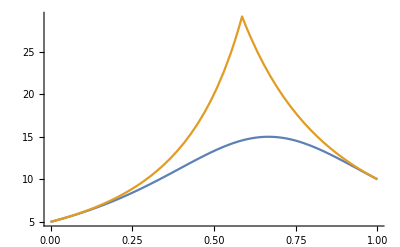

```mathematica
Plot[{T//.{t0->5,t1->10},T2 //.{t0->5,t1->10}},{q,0,1}]
```

```mathematica
f = Exp[-A(t1+q^2C)]+Exp[-A(t0+(1-q)^2 C)]
```

ⅇ^(-A (C (1-q)^2+t0))+ⅇ^(-A (C q^2+t1))

```mathematica
D[f,q]
```

2 A C ⅇ^(-A (C (1-q)^2+t0)) (1-q)-2 A C ⅇ^(-A (C q^2+t1)) q

```mathematica
Plot[1/((1-q)^2+q^2),{q,0,1}]
```

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[D == a^2/(2*V*n+2*b*a/3),a]
```

{{a→1/3 (b D-√(b^2 D^2+18 D n V))},{a→1/3 (b D+√(b^2 D^2+18 D n V))}}

```mathematica
d  = Exp[-a^2/(2 V+2 b a/3)]
```

ⅇ^(-a^2/((2 a b)/3+2 V))

```mathematica
Solve[D == n*a^2/(2 V+2 b a/3),a]
```

{{a→(b D-√(b^2 D^2+18 D n V))/(3 n)},{a→(b D+√(b^2 D^2+18 D n V))/(3 n)}}

```mathematica
Simplify[(x/y)/z]
```

x/(y z)

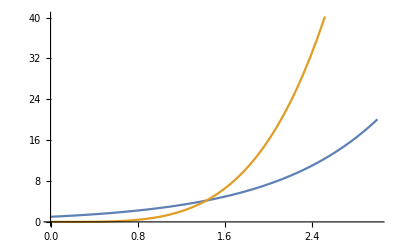

```mathematica
Plot[{Exp[x],x^4},{x,0,3}]
```

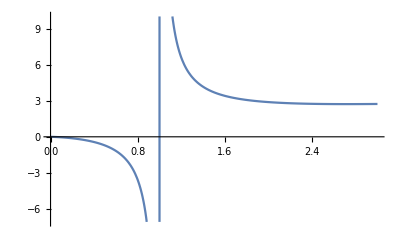

```mathematica
Plot[x/Log[x],{x,0,3}]
```

```mathematica
Solve[x == n Log[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-n ProductLog[-1/n]}}

```mathematica
Together[h/m+m]
```

(h+m^2)/m

```mathematica
Solve[h-m == h/m,h]
```

{{h→m^2/(-1+m)}}

```mathematica
Solve[m^2/(-1+m)==m+x,x]
```

{{x→m/(-1+m)}}

```mathematica
Solve[m/(-1+m) == 1+ x,x]
```

{{x→1/(-1+m)}}

```mathematica
Solve[1/(-1+m)==1/m+x,x]
```

{{x→1/((-1+m) m)}}

```mathematica
Reduce[m^2/(m-1)<2m,m]
```

0<m<1||m>2

```mathematica
Solve[Exp[-n*a^2/(2(p+a/3))] == d,a]
```

{{a→ConditionalExpression[(2 ⅈ π C[1]+Log[1/d]-√(18 n p (2 ⅈ π C[1]+Log[1/d])+(2 ⅈ π C[1]+Log[1/d])^2))/(3 n),C[1]∈Integers]},{a→ConditionalExpression[(2 ⅈ π C[1]+Log[1/d]+√(18 n p (2 ⅈ π C[1]+Log[1/d])+(2 ⅈ π C[1]+Log[1/d])^2))/(3 n),C[1]∈Integers]}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Solve[D[d+k*Exp[-h*d^2/(24m)],d]==0,d]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{d→-(2 ⅈ √3 √m √ProductLog[-(12 m)/(h k^2)])/(√h)},{d→(2 ⅈ √3 √m √ProductLog[-(12 m)/(h k^2)])/(√h)}}

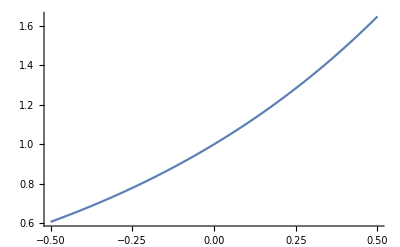

```mathematica
Plot[Exp[x],{x,-.5,.5}]
```

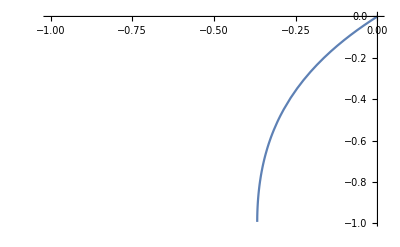

```mathematica
Plot[ProductLog[x],{x,-1,0}]
```

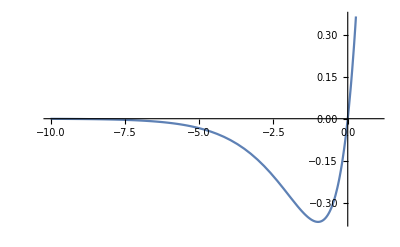

```mathematica
Plot[w*Exp[w],{w,-10,1}]
```

```mathematica
D[w Exp[w],w]
```

```mathematica
Solve[ⅇ^w+ⅇ^w w==0,w]
```

{{w→-1}}

```mathematica
-1 Exp[-1]
```

-1/ⅇ

```mathematica
2.71828459045
```

```mathematica
{{d->-(2 ⅈ √3 √m √ProductLog[-(12 m)/(h k^2)])/(√h)},{d->(2 ⅈ √3 √m √ProductLog[-(12 m)/(h k^2)])/(√h)}}/.Rule->Equal
```

```mathematica
{{d==-(2 ⅈ √3 √m √ProductLog[-(12 m)/(h k^2)])/(√h)rm{d==(2 ⅈ √3 √m √ProductLog[-(12 m)/(h k^2)])/(√h)}}
```

```mathematica
Normal[Solve[k Exp[-h d^2/(24m)]== 1/h,d,Reals]]
```

{{d→-2 √6 √((m Log[h k])/h)},{d→2 √6 √((m Log[h k])/h)}}

```mathematica
c
```

```mathematica
Normal[%]
```

{{d→-(2 √6 √m √(2 ⅈ π C[1]+Log[h k]))/(√h)},{d→(2 √6 √m √(2 ⅈ π C[1]+Log[h k]))/(√h)}}

```mathematica
R = h+T(Sqrt[(24m Log[T K])/h] + 1/h)
```

h+T (1/h+2 √6 √((m Log[K T])/h))

```mathematica
Solve[D[h+T(Sqrt[(24m Log[T K])/h] ),h]==0,h]
```

{{h→-(-6)^(1/3) m^(1/3) T^(2/3) Log[K T]^(1/3)},{h→6^(1/3) m^(1/3) T^(2/3) Log[K T]^(1/3)},{h→(-1)^(2/3) 6^(1/3) m^(1/3) T^(2/3) Log[K T]^(1/3)}}

```mathematica
Simplify[R /. h->m^(1/3) T^(2/3) Log[K T]^(1/3)]
```

2 √6 T √((m^(2/3) Log[K T]^(2/3))/T^(2/3))+T^(1/3)/(m^(1/3) Log[K T]^(1/3))+m^(1/3) T^(2/3) Log[K T]^(1/3)

```mathematica
1/h /. h ->6^{1/3}m^(1/3) T^(2/3) Log[K T]^(1/3)
```

{1/(6^(1/3) m^(1/3) T^(2/3) Log[K T]^(1/3))}

```mathematica
N[3*6^(1/3)]
```

5.45136

```mathematica
N[2 Sqrt[6]+1]
```

5.89898

```mathematica
N[1/6^(1/3)]
```

0.550321

```mathematica
N[2^{1/3}*Log[2]^{1/3}]
```

{1.11503}